```mathematica
Subscript[m, N]=940;ℏc=197.327;
V0=35;R=2;a=0.5;μ=8/9 Subscript[m, N];
rmax=4.0;dr=0.01;
rlist=Range[0,rmax,dr];
n=Length[rlist]
```

401

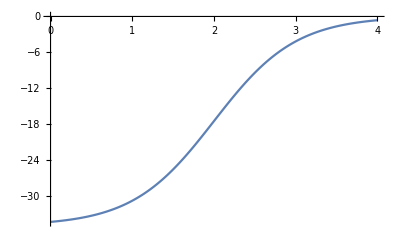

```mathematica
V[r_]:=-V0/(1+Exp[(r-R)/a]);
Vmat=DiagonalMatrix[V[rlist]];
ListLinePlot[V[rlist],DataRange->{0,rmax}]
```

```mathematica
(*calculate Hamiltonian matrix*)
one[n_,d_]:=
DiagonalMatrix[1+0Range[n-Abs[d]],d];
KE=-ℏc^2/(2 μ) 1/dr^2(one[n,-1]-2 one[n,0]+one[n,1]);
H0=KE+Vmat;
```

```mathematica
(*{eval,evec}=Eigensystem[H0];
Manipulate[ListPlot[{rlist,evec⟦-i⟧}ᵀ,Joined->True,PlotRange->All],{i,1,n,1}]*)
```

```mathematica
k[En_]:=Sqrt[-(2μ En)/ℏc^2]
```

```mathematica
En=V0/2;En1=1;
```

```mathematica
k[V0/2]
```

0.+0.866633 ⅈ

```mathematica
H[[n,n]]=Vmat[[n,n]]+-ℏc^2/(2 μ) 1/dr^2(dr k[En]-1);{eval,evec}=Eigensystem[H];
```

```mathematica
Manipulate[ListLinePlot[{Transpose[{rlist,Abs[evec⟦-i⟧]}]},PlotRange->All],{i,1,n,1}]
```

```mathematica
eval[[-4]]
```

157.661-10.9634 ⅈ

```mathematica
While[Abs[En/En1]≥1.0001||Abs[En/En1]≤0.9999,H=H0;H[[n,n]]=Vmat[[n,n]]+-ℏc^2/(2 μ) 1/dr^2(dr k[En]-1);{eval,evec}=Eigensystem[H];En1=En;En=eval[[-1]];]
```

```mathematica
En
```

-7.36002

```mathematica
wave[En_,r_]:=Exp[-k[En] r]
```

```mathematica
const[i_]:=evec[[-i,-1]]/wave[eval[[-i]],rmax]
```

```mathematica
Manipulate[ListLinePlot[{Transpose[{rlist,evec⟦-i⟧}],Transpose[{Range[rmax,10,dr],const[i] wave[eval[[-i]],Range[rmax,10,dr]]}]},PlotRange->All],{i,1,n,1}]
```

Part::partd: Part specification evec⟦-1⟧ is longer than depth of object.

Transpose::nmtx: The first two levels of {rlist,evec⟦-1⟧} cannot be transposed.

Range::range: Range specification in Range[rmax,10,dr] does not have appropriate bounds.

Part::partd: Part specification eval⟦-1⟧ is longer than depth of object.

Range::range: Range specification in Range[rmax,10,dr] does not have appropriate bounds.

Transpose::nmtx: The first two levels of {Range[rmax,10,dr],const[1] wave[eval⟦-1⟧,Range[rmax,10,dr]]} cannot be transposed.

Range::range: Range specification in Range[rmax,10.,dr] does not have appropriate bounds.

General::stop: Further output of Range::range will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {Range[rmax,10.,dr],const[1.] wave[eval⟦-1⟧,Range[rmax,10.,dr]]} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Part::partd: Part specification evec⟦-1⟧ is longer than depth of object.

Transpose::nmtx: The first two levels of {{0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,«15»,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,«351»},«1»} cannot be transposed.

Part::partd: Part specification eval⟦-1⟧ is longer than depth of object.

Transpose::nmtx: The first two levels of {{4.,4.01,4.02,4.03,4.04,4.05,4.06,4.07,4.08,4.09,4.1,4.11,4.12,4.13,4.14,4.15,4.16,4.17,4.18,4.19,4.2,4.21,«7»,4.29,4.3,4.31,4.32,4.33,4.34,4.35,4.36,4.37,4.38,4.39,4.4,4.41,4.42,4.43,4.44,4.45,4.46,4.47,4.48,4.49,«551»},«1»} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

$Aborted

Transpose::nmtx: The first two levels of {{4.,4.01,4.02,4.03,4.04,4.05,4.06,4.07,4.08,4.09,4.1,4.11,4.12,4.13,4.14,4.15,4.16,4.17,4.18,4.19,4.2,4.21,«7»,4.29,4.3,4.31,4.32,4.33,4.34,4.35,4.36,4.37,4.38,4.39,4.4,4.41,4.42,4.43,4.44,4.45,4.46,4.47,4.48,4.49,«551»},«1»} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

ListLinePlot::lpn: {{{0.,0.000709868-0.0000295922 ⅈ},{0.01,0.00141965-0.0000591753 ⅈ},{0.02,0.00212927-0.0000887404 ⅈ},«46»,{0.49,0.0338063-0.00129663 ⅈ},«351»},Transpose[{{«1»},«1»}]} is not a list of numbers or pairs of numbers.